## Brian — PS 20 — 2025-04-22 — Solution

## EIWL3 Sections 45 and 46

## Exercises from EIWL3 Section 45

```mathematica
(* For a bunch of the exercises, we need to have defined: *)

planets=CloudGet["http://wolfr.am/7FxLgPm5"]
```

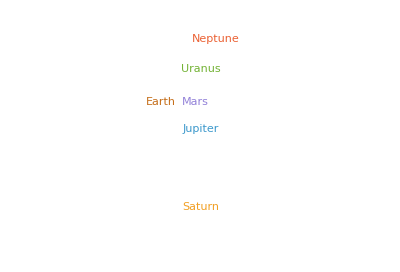

```mathematica
(* 45.1 *) WordCloud[planets[All,"Moons",Length]]
```

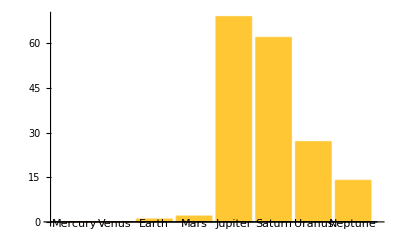

```mathematica
(* 45.2 *)BarChart[planets[All,"Moons",Length],ChartLabels->Automatic]
```

```mathematica
(* 45.3 *)planetsSortedByNumberOfMoonsDescending=Reverse[planets[SortBy[Length[#Moons]&]]];
planetsSortedByNumberOfMoonsDescending[All,"Mass"]
```

```mathematica
(* 45.4 *) allMoons = planets[All,"Moons"]
(* the preceding table was not asked for (just practicing) *)
(* the following table is what was asked for *)
planets[All,"Moons",Max,"Mass"]
```

```mathematica
planets[All,"Moons","Mass"]
```

```mathematica
(* 45.5 *) Sort[planets[All,"Moons",Max,"Mass"]]
```

```mathematica
(* 45.6 *) planets[All,"Moons",Median,"Mass"]
```

```mathematica
(* 45.7 *) earthMass=Entity["Planet","Earth"][EntityProperty["Planet","Mass"]];
```

```mathematica
planet[All,"Moons",Select[#>0.0001 earthMass&]]
```

## Exercises from EIWL3 Section 46

```mathematica
(* 46.1 *) Spectrogram[SpeechSynthesize[IntegerName[123456]]]
```

-Graphics-

```mathematica
(* 46.2 *) Spectrogram[SpeechSynthesize[SortBy[WordList[],StringLength[#]&][[-1]]]]
```

-Graphics-

```mathematica
(* 46.3 *) spokenAlphabet=SpeechSynthesize[StringRiffle[Alphabet[]," "]]
```

```mathematica
(* 46.4 *) SpeechSynthesize[spokenAlphabet]
```

```mathematica
(* 46.5 *) AudioPitchShift[SpeechSynthesize["hello"],2]
```

```mathematica
(* 46.6 *) Table[AudioPitchShift[SpeechSynthesize["computer"],r],{r,1.0,1.5,0.1}]
```

{,,,,,}

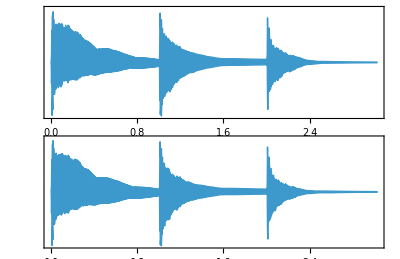

```mathematica
(* 46.7 *) AudioPlot[Sound[Table[SoundNote[note,1,"Guitar"],{note,{0,12,24}}]]]
```

```mathematica
(* 46.8 *) Table[AudioIdentify[AudioPitchShift[SoundNote[0,1,"Trumpet"],r]],{r,0.5,1.0,0.1}]
```

{trombone,trombone,trombone,trumpet,trumpet,trumpet}

```mathematica
(* 46.9 *) foxImage=Entity["TaxonomicSpecies","VulpesVulpes::48y38"][EntityProperty["TaxonomicSpecies","Image"]];
AnimationVideo[Blur[foxImage,20-step],{step,0,20}]
```

```mathematica
(* 46.10 *) AnimationVideo[Graphics[{Circle[],RegularPolygon[vertices]}],{vertices,3,20}]
```

```mathematica
(* 46.11 *) AnimationVideo[Graphics[{Hue[hue],Disk[]},ImageSize->50],{hue,0,1}]
```

```mathematica
(* 46.12 *) AnimationVideo[Graphics[Rasterize[letter,RasterSize->200]],{letter,Capitalize[Alphabet[]]},FrameRate->2]
```